```mathematica
ClearAll["Global`*"]
```

# Decision Tree (with Regression)

In this Notebook, utilize a decision tree-like algorithm for creating a model for the COVID severity index.

## Data Import

Here we will import the time-series data and the compiled data that will be used for the machine learning models.

## File Paths

```mathematica
hereDir=NotebookDirectory[];
projDir=ParentDirectory[hereDir];
compDataFile=FileNameJoin[{projDir,"RawDataToUsableDataConverter","src","FinalCombinedFeaturesWithSeverity.csv"}];
timeSeriesFile=FileNameJoin[{projDir,"RawDataToUsableDataConverter","src","StartingFiles","CovidFileWithDates.csv"}];
```

## Import Data

The compiled data has information in the following order:
1. COVID Severity Index
2. FIPS County Code
3. Total Votes (2016)
4. Votes for Democratic Candidate (2008)
5. Votes for Democratic Candidate (2012)
6. Votes for Republican Candidate (2008)
7. Votes for Republican Candidate (2012)
8. Percentage of Votes for Democratic Candidate (2016)
9. Percentage of Votes for Republican Candidate (2016)
10. Percentage of Votes for Republican Candidate (2012)
11. Percentage of Votes for Republican Candidate (2008)
12. Percentage of Votes for Democratic Candidate (2012)
13. Percentage of Votes for Democratic Candidate (2008)
14. Percentage of Adults with Less Than a High School Diploma (Exit Poll 2016 Election)
15. Percentage of Adults with at Least a High School Diploma (Exit Poll 2016 Election)
16. Percentage of Adults with at Least a Bachelor’s Degree (Exit Poll 2016 Election)
17. Percentage of Adults with at Least a Graduate Degree (Exit Poll 2016 Election)
18. School Enrollment (???)
19. Percentage of Children Under 6 Living in Poverty (2016 Estimate)
20. Percentage of Adults 65 and Older Living in Poverty (2016 Estimate)
21. Total Population (2016 Estimate)
22. Poverty Rate Below Federal Poverty Threshold (2016 Estimate)
23. Percentage of People in Management, Professional, and Related Occupations (2016 Estimate)
24. Percentage of People in Service Occupations (2016 Estimate)
25. Percentage of People in Sales and Office Occupations (2016 Estimate)
26. Percentage of People in Farming, Fishing, and Forestry Occupations (2016 Estimate)
27. Percentage of People in Construction, Extraction, Maintenance, and Repair Occupations (2016 Estimate)
28. Percentage of People in Production, Transportation, and Material Moving Occupations (2016 Estimate)

The time-series data has entries in the following order:
1. Date (yyyy-mm-dd)
2. County Name
3. State Name
4. FIPS Code
5. Cumulative Number of Cases
6. Cumulative Number of Deaths

```mathematica
compData=Import[compDataFile,"Table","FieldSeparators"->";"];
timeSeriesData=Import[timeSeriesFile];
```

## Data “Binarization”

Here we will convert the original feature vectors to binary feature vectors based on the median value of each feature (0 corresponds to ≤ the median, 1 corresponds to > the median).

```mathematica
toBinaryData[origData_]:=(* Converts the original data to binary, each feature is 0 if it is less than the median and 1 if it is larger *)
Module[{binaryData,medians,featureLength,sampleCount,i,j},
binaryData=0*origData; (* Allocate memory to the array that will contain the binary data *)
medians=0*origData[[1]]; (* Allocate memory to the array that will store the median of each feature *)

featureLength=Length[origData[[1]]]; (* Length of the feature vector with label and FIPs code included *)
sampleCount=Length[origData[[;;,1]]]; (* Number of samples in the original data *)
(* Find the median of each entry in the feature vector *)
For[i = 1,i≤featureLength,i++,
medians[[i]]=Median[origData[[;;,i]]];
];

For[j=1,j≤sampleCount,j++, (* Convert each entry to binary *)
(* We will convert each feature to binary and fix the ones we do not want in binary afterward *)
For[i = 1,i≤featureLength,i++,
If[origData[[j,i]]≤medians[[i]],
binaryData[[j,i]]=0, (* 0 if ≤ median *)
binaryData[[j,i]]=1 (* 1 if > median *)
]
];

binaryData[[;;,2]]=origData[[;;,2]];

];

(* Copy the FIPs code to the binary feature vectors *)
binaryData[[;;,2]]=origData[[;;,2]]; 

Return[binaryData,Module];
]

toBinarySample[origData_,sample_]:=(* Returns the binarized sample *)
Module[{binarySample,medians,featureLength},
binarySample=0*sample; (* Array to store the binarized sample *)
medians=0*origData[[1]]; (* Allocate memory to the array that will store the median of each feature *)

featureLength=Length[origData[[1]]]; (* Length of the feature vector with label and FIPs code included *)
(* Find the median of each entry in the feature vector *)
For[i = 1,i≤featureLength,i++,
medians[[i]]=Median[origData[[;;,i]]];
];

(* We will convert each feature to binary and fix the ones we do not want in binary afterward *)
For[i = 3,i≤featureLength,i++,
If[sample[[i]]≤medians[[i]],
binarySample[[i]]=0, (* 0 if ≤ median *)
binarySample[[i]]=1 (* 1 if > median *)
];
];

(* Copy the FIPs code to the binary sample, and we ignore the label *)
binarySample[[2]]=sample[[2]];

Return[binarySample,Module]
]
```

```mathematica
toOrigData[origData_,binaryData_]:=(* Returns the original data entries corresponding to the FIPs codes in the binary data *)
Module[{origDataSubset,binarySampleCount,featureCount,pattern,i},
origDataSubset = 0*binaryData;(* Subset of the original data that we will return *)
binarySampleCount=Length[binaryData[[;;,1]]]; (* Number of samples in the binary data *)
featureCount=Length[binaryData[[1]]]; (* Number of features in the feature vector, including label and FIPs code *)
pattern=Table[_,{j,1,featureCount,1}]; 

(* Pattern to use to pick out the original sample from the original data set *)
For[i=1,i≤binarySampleCount,i++, (* Loop trhrough all of the samples in the binary data *)
pattern[[2]]=binaryData[[i,2]]; (* FIPs code of the binary sample *)
origDataSubset[[i]]=Flatten[Cases[origData,pattern]](* Find the sample in the original data set with the same FIPs code as the binary sample *)
];

Return[origDataSubset,Module]
]
```

## Calculating Mutual Information

Here we will calculate the mutual information between the j^th binary feature and the binary label.

```mathematica
probDists[x_,y_]:=Module[{probX,probY,probTotal,condProb,condProbTotal}, (* Computes the discrete probability distributions needed to calculate the mutual information *)
probX = {0,0}; (* Probability distribution of feature in x, {x = 0, x = 1} *)
probY={0,0}; (* Probability distribution of y {y = 0, y = 1} *)
probTotal=0; (* Number of samples that count to the probability distribution of feature in x *)
condProb={0,0,0,0}; (* Condition probability distribution of feature in x given y, {x = 0 | y = 0, x = 1 | y = 0, x = 0 | y = 1, x = 1 | y = 1} *)
condProbTotal={0,0};(* Number of samples that count to the conditional probability distribution of feature in x given y, {y = 0, y = 1} *)
For[i=1,i≤Length[x],i++, (* Loop through the samples *)
probTotal=probTotal+1; (* Every sample counts towards the probability distribution of feature in x *)
If[x[[i]] == 0,
probX[[1]]=probX[[1]]+1;
If[y[[i]]==0, (* Contributes to the conditional probability of x given y = 0 *)
condProb[[1]]=condProb[[1]]+1;
condProbTotal[[1]]=condProbTotal[[1]]+1,
condProb[[3]]=condProb[[3]]+1;
condProbTotal[[2]]=condProbTotal[[2]]+1
],
probX[[2]]=probX[[2]]+1;
If[y[[i]]==0, (* Contributes to the conditional probability of x given y = 0 *)
condProb[[2]]=condProb[[2]]+1;
condProbTotal[[1]]=condProbTotal[[1]]+1,
condProb[[4]]=condProb[[4]]+1;
condProbTotal[[2]]=condProbTotal[[2]]+1
]
];
If[y[[i]]==0, (* Tally up y = 0, y = 1 *)
probY[[1]]=probY[[1]]+1,
probY[[2]]=probY[[2]]+1
]
];
(* Calculate the probabilities *)
If[probTotal≠0,
probX = probX/probTotal;
probY=probY/probTotal,
probX=0;
probY=0
];
If[condProbTotal[[1]]≠0,
condProb[[1;;2]] = condProb[[1;;2]]/condProbTotal[[1]],
condProb[[1;;2]] =0
];
If[condProbTotal[[2]]≠0,
condProb[[3;;4]] = condProb[[3;;4]]/condProbTotal[[2]],
condProb[[3;;4]]=0
];
Return[{probX,probY,condProb},Module]
]
```

```mathematica
mutualInfo[probDist_]:=Module[{entropy,condEntropy},(* Calculates mutual information of a feature x given a label y, given the probability distribution of x and conditional probability distribution of x given y *)
entropy = 0; (* Entropy of x *)
If[Min[probDist[[1]]]≠0,
entropy = -Sum[probDist[[1,i]]*Log[2,probDist[[1,i]]],{i,1,2}],
Return[0,Module]
];
condEntropy=0;(* Conditional entropy of x given y *)
If[Min[probDist[[3]]]≠0,
condEntropy=-Sum[probDist[[2,i]]*Sum[probDist[[3,j+2*(i-1)]]*Log[2,probDist[[3,j+2*(i-1)]]],{j,1,2}],{i,1,2}],
Return[0,Module]
];
Return[entropy-condEntropy+0.0,Module]
]
```

## Decision Tree Creation

In this section, we will create the decision tree using the binary labels and features, and at each leaf we will hold the subset of training data that we will then use for linear regression for the sample.

```mathematica
calculateNode[inData_]:=(* Using the subset of data given, determine which binary feature should be split. Returns the feature index (excluding label and FIPs code) of the feature to split the node on *)
Module[{featureLength,info,dists,i}, 
featureLength=Length[inData[[1]]]; (* Number of features including label and FIPs code *)
info=Table[0,{i,1,featureLength-2,1}]; (* Stores the mutual information for each feature *)

For[i=3,i≤featureLength,i++, (* Calculate the mutual information for each vector, start at the first actual feature *)
dists=probDists[inData[[;;,i]],inData[[;;,1]]];
info[[i-2]]=mutualInfo[dists];
];

If[Max[info]<1.0×10^-2,(* If the mutual information is small, we don't propagate the tree any more *)
Return[inData],(* If we don't have mutual information left, we just put the subset of data here *)
Return[Ordering[info,-1][[1]]] (* If we have sizeable mutual information, return the feature index excluding label and FIPs code *)
];
]
```

```mathematica
makeDecisionTree[origData_]:=(* Computes a decision tree from the input data (not binarized), assuming the first entry of each sample is the severity index and the second is the FIPs code *)Module[{binaryData,featureLength,info, dists,i,j,k,l,splitPos,pattern,tree,traverseList,currentNode,currentData,childVal,prevLength,counter},
binaryData=toBinaryData[origData];
featureLength=Length[binaryData[[1]]];(* Number of features including label and FIPs code *)
dists = {}; (* Stores the probability distribution needed for computing the mutual information needed for each subset of data *)
info=Table[0,{i,1,featureLength-2,1}]; (* Stores the mutual information for each feature *)
splitPos=0; (* Feature to split the data on *)

(* Create the first split *)
For[i=3,i≤featureLength,i++, 
dists=probDists[binaryData[[;;,i]],binaryData[[;;,1]]];
info[[i-2]]=mutualInfo[dists];
];
splitPos = Ordering[info,-1][[1]]; (* Get the index, excluding the label and FIPs code, where the split should be *)

(* Create the decision tree *)
tree=CreateDataStructure["BinaryTree",splitPos->{Null,Null}];
traverseList={}; (* List of nodes to keep track of traversal, the last entry is the node we are currently at and which node to traverse down to get to the current node *)
AppendTo[traverseList,{tree,Null}];
currentNode=traverseList[[-1,1]]; (* Current node to check *)
pattern=Table[_,{i,1,featureLength,1}]; (* Pattern to sort through the binary data *)
pattern[[splitPos+2]]=0;
currentData=Cases[binaryData,pattern];

counter = 0; (* We use a counter to make sure the function doesn't go on forever. Since the data set is small, we can adjust the bound for the counter on the fly *)

While[(Length[traverseList]>0)∧(counter ≤ 5000),

counter = counter + 1;
prevLength=Length[traverseList]; (* Save the traversal list length to make sure it changes each step *)
(*Print[StringJoin["Begin loop traverse list: ", ToString[traverseList[[;;,2]]]]];*)

(* I apologize now for how sloppy this code is. There's definitely a better way to do this. I thought using Mathematica would be faster for the homework, but I'm finding myself more comfortable with C++ nowadays. *)
(* Check the left node *)
(*Print["Checking left child..."];*) (* There's no good debugging options for Mathematica, so print statements are all that's left *)
If[currentNode["LeftNullQ"], (* If the left child is null, calculate the value that goes there *)
pattern = Table[_,{i,1,featureLength,1}]; (* Update the pattern to get the subset of data that we want *)
If[Length[traverseList]>1,
For[i=1,i≤Length[traverseList]-1,i++,
If[traverseList[[i,2]]==="Left", 
pattern[[traverseList[[i,1]]["Data"]+2]] = 0,
pattern[[traverseList[[i,1]]["Data"]+2]]=1
]
]
];
pattern[[traverseList[[-1,1]]["Data"]+2]]=0; (* Searching to the left of the current node *)
(*Print[StringJoin["Left pattern: ", ToString[pattern]]];*)
currentData=Cases[binaryData,pattern];
childVal=calculateNode[currentData];
currentNode["SetLeft",CreateDataStructure["BinaryTree",childVal->{Null,Null}]];

(* If we fill in the left node with a number, we should move to it and go through the While body again *)
If[(childVal[[0]]===Integer)∨(childVal[[0]]===Real),
traverseList[[-1,2]]="Left"; (* We head left from the current node *)
AppendTo[traverseList,{currentNode["Left"], Null}];
currentNode=currentNode["Left"];
Continue[]
(* If we fill in the left node with a list, we should check the right node *)
]
];

(* Check the right node *)
(*Print["Checking right child..."];*)
If[currentNode["RightNullQ"], (* If the right child is null, calculate the value that goes there *)
pattern = Table[_,{i,1,featureLength,1}]; (* Update the pattern to get the subset of data that we want *)
If[Length[traverseList]>1,
For[i=1,i≤Length[traverseList]-1,i++,
If[traverseList[[i,2]]==="Left", 
pattern[[traverseList[[i,1]]["Data"]+2]] = 0,
pattern[[traverseList[[i,1]]["Data"]+2]]=1
]
]
];
pattern[[traverseList[[-1,1]]["Data"]+2]]=1; (* Searching to the right of the current node *)
(*Print[StringJoin["Right pattern: ", ToString[pattern]]];*)
currentData=Cases[binaryData,pattern];
childVal=calculateNode[currentData];
currentNode["SetRight",CreateDataStructure["BinaryTree",childVal->{Null,Null}]];

(* If we fill in the right node with a number, we should move to it and go through the While body again *)
If[(childVal[[0]]===Integer)∨(childVal[[0]]===Real),
traverseList[[-1,2]]="Right"; (* We head right from the current node *)
AppendTo[traverseList,{currentNode["Right"], Null}];
currentNode=currentNode["Right"];
Continue[],
(* If we fill in the right node with a list, we should move up to the parent of the current node *)
If[Length[traverseList]>1, (* If there's a parent node to move up to, move up to it *)
currentNode=traverseList[[-2,1]];
traverseList[[-2,2]]=Null
];
traverseList=Drop[traverseList,-1]
], (* If right is not null, we need to back up if we can *)
If[Length[traverseList]>1, (* If there's a parent node to move up to, move up to it *)
currentNode=traverseList[[-2,1]];
traverseList[[-2,2]]=Null
];
traverseList=Drop[traverseList,-1]
];

(*Print[StringJoin["End loop traverse list: ", ToString[traverseList[[;;,2]]]]];*)

If[prevLength == Length[traverseList], (* If the traverse list length doesn't change, abort the loop *)
traverseList={}
]
];

Return[tree,Module]
]
```

## Sample Evaluation

Here we will use our decision tree to create a predicted label for our sample.

```mathematica
returnSubset[decTree_,sample_]:=Module[(* Gives the subset of the data used for the linear regression for the given sample (binarized). *)
{counter,currentNode,outSubset}, 
outSubset={}; (* Subset of data we will use for linear regression with our sample *)
counter = 0; (* Counter to ensure the while loop terminates *)
currentNode=decTree; (* The current node we are on in the tree *)
While[(outSubset==={})∧(counter ≤ 20),
If[sample[[currentNode["Data"]+1]]==0, (* Feature split by the current node is 0 *)
If[(((currentNode["Left"])["Data"])[[0]]===Integer)∨(((currentNode["Left"])["Data"])[[0]]===Real),(* If the left child is a number, move to it *)
currentNode = currentNode["Left"];
Continue[],
(* If the left child is a subset of the data, assign it to the label *)
outSubset=ToExpression[(currentNode["Left"])["Data"]];
Continue[]
],
(* Feature split by the current node is 1 *)
If[(((currentNode["Right"])["Data"])[[0]]===Integer)∨(((currentNode["Right"])["Data"])[[0]]===Real),(* If the right child is a number, move to it *)
currentNode = currentNode["Right"];
Continue[],
(* If the right child is a subset of the data, assign it to the label *)
outSubset=ToExpression[(currentNode["Right"])["Data"]];
Continue[]
]
];
counter = counter + 1;
];
Return[outSubset,Module]
]
```

```mathematica
evalSample[origData_,decTree_,sample_]:=Module[(* Returns the input sample with the predicted label *)
{binarySample,binarySampleSubset,sampleSubset,subsetLabels,subsetFeatures,sampleFeatures,outLabel,outSample},
binarySample=toBinarySample[origData,sample]; (* Binarized sample, for finding subset of data given by the decision tree *)
binarySampleSubset=returnSubset[decTree,sample]; (* The subset of data we will use for the linear regression, based on the decision tree (binarized) *)

sampleSubset=toOrigData[origData,binarySampleSubset]; (* Get the subset of original data corresponding to the subset of binary data *)

subsetLabels = sampleSubset[[;;,1]]; (* Labels of the samples in the subset of data, not binary *)
subsetFeatures=sampleSubset[[;;,3;;]]; (* Features of the samples in the subset of data, not binary *)
sampleFeatures=sample[[3;;]]; (* Feature vector for the sample, assuming first entry is label and second entry is FIPs code *)
outLabel={sampleFeatures}.Inverse[Transpose[subsetFeatures].subsetFeatures].Transpose[subsetFeatures].Transpose[{subsetLabels}]; (* Predicted label for the sample, some of the vectors are trasposed of what we would like them to be, so the equation is a little different *)

outSample=sample; (* We return the sample along with the predicted label *)
outSample[[1]]=Flatten[outLabel][[1]];

Return[outSample, Module]
]
```

## K-Fold Cross Validation

In this section, we write code to perform a K-Fold cross validation of our tree.

```mathematica
crossValidation[origData_,k_]:=(* Returns the average error of a k-fold cross-validation for the decision tree *)
Module[{sampleData,folds,error,foldCount,i,testingData,trainingData,decisionTree,testingCount,j,predLabel,avgErr},
sampleData=RandomSample[origData]; (* Randomize the order of the data *)
folds=Partition[sampleData,Floor[Length[sampleData]/k]]; (* Partitions of the training data into about k partitions*)
foldCount=k; (* Number of folds *)
avgErr=0; (* Average error of a single tree *)
error=0;

For[i=1,i≤foldCount,i++,(* Go through each fold *)
testingData=folds[[i]]; (* The fold to be tested *)
trainingData=Complement[sampleData,testingData]; (* The data to train our model on *)
decisionTree=makeDecisionTree[trainingData]; (* Make a decision tree based on the training data *)
testingCount=Length[testingData]; (* Number of samples in the training data *)
For[j=1,j≤testingCount,j++,
predLabel=evalSample[trainingData,decisionTree,testingData[[j]]][[1]]; (* Predicted label for the sample *)
avgErr=avgErr + (Abs[predLabel-testingData[[j,1]]]); (* Add the accuracies together *)
];
avgErr=avgErr/testingCount;(* Average error of the tree *)
error = error + avgErr; (* Add the average error of the tree to the error we return *)
avgErr=0; (* Reset the error of the tree to 0 *)
];
error = error/foldCount; (* Average the average accuracies over each fold *)
Return[error,Module]
]
```

## Evaluation Testbed

We do test evaluations here during and after development.

## Accuracy Testing

```mathematica
validationResults=Table[crossValidation[compData,10],{i,1,10}]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.20157×10^12,1.00557×10^12,9.49478×10^11,3.01611×10^11,2.81668×10^11,7.55789×10^7,1.6664×10^8,7.07665×10^7,7.17955×10^7,1.77549×10^8,1.76391×10^8,4.6601×10^7,2.04422×10^8,5.73645×10^7,2.25137×10^7,1.94949×10^8,8.54273×10^7,3.48841×10^7,2.78038×10^12,5.52262×10^7,1.20551×10^6,8.06092×10^7,5.17856×10^7,6.47838×10^7,759990.,1.85278×10^7,3.45564×10^7},«25»,{3.45564×10^7,2.65315×10^7,2.53458×10^7,1.06392×10^7,«19»,6026.57,192.902,1963.48,3390.62}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

```mathematica
Mean[validationResults]
StandardDeviation[validationResults]
```

3.88139

2.03245

## Decision Tree Visualization

We will make a plot of the first five layers of the fully-trained decision tree.

```mathematica
ds = makeDecisionTree[compData];
```

```mathematica
deleteChildren[node_]:=(* Deletes both children of a node *)
Module[{},
node["SetLeft",CreateDataStructure["BinaryTree",]];
node["SetRight",CreateDataStructure["BinaryTree",]];
Return[node,Module]
]
```

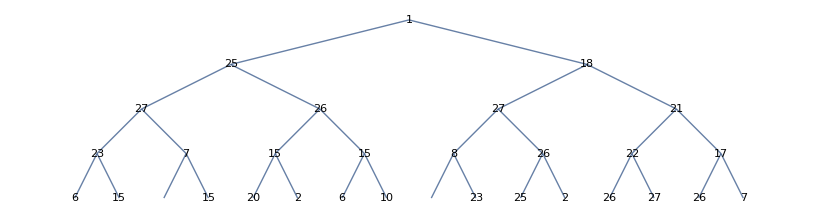

```mathematica
dsCopy=ds;

dsCopy["Left"]["Left"]["Left"]["Left"]=deleteChildren[dsCopy["Left"]["Left"]["Left"]["Left"]];
dsCopy["Left"]["Left"]["Left"]["Right"]=deleteChildren[dsCopy["Left"]["Left"]["Left"]["Right"]];
dsCopy["Left"]["Left"]["Right"]["Left"]=deleteChildren[dsCopy["Left"]["Left"]["Right"]["Left"]];
dsCopy["Left"]["Left"]["Right"]["Right"]=deleteChildren[dsCopy["Left"]["Left"]["Right"]["Right"]];
dsCopy["Left"]["Right"]["Left"]["Left"]=deleteChildren[dsCopy["Left"]["Right"]["Left"]["Left"]];
dsCopy["Left"]["Right"]["Left"]["Right"]=deleteChildren[dsCopy["Left"]["Right"]["Left"]["Right"]];
dsCopy["Left"]["Right"]["Right"]["Left"]=deleteChildren[dsCopy["Left"]["Right"]["Right"]["Left"]];
dsCopy["Left"]["Right"]["Right"]["Right"]=deleteChildren[dsCopy["Left"]["Right"]["Right"]["Right"]];
dsCopy["Right"]["Left"]["Left"]["Left"]=deleteChildren[dsCopy["Right"]["Left"]["Left"]["Left"]];
dsCopy["Right"]["Left"]["Left"]["Right"]=deleteChildren[dsCopy["Right"]["Left"]["Left"]["Right"]];
dsCopy["Right"]["Left"]["Right"]["Left"]=deleteChildren[dsCopy["Right"]["Left"]["Right"]["Left"]];
dsCopy["Right"]["Left"]["Right"]["Right"]=deleteChildren[dsCopy["Right"]["Left"]["Right"]["Right"]];
dsCopy["Right"]["Right"]["Left"]["Left"]=deleteChildren[dsCopy["Right"]["Right"]["Left"]["Left"]];
dsCopy["Right"]["Right"]["Left"]["Right"]=deleteChildren[dsCopy["Right"]["Right"]["Left"]["Right"]];
dsCopy["Right"]["Right"]["Right"]["Left"]=deleteChildren[dsCopy["Right"]["Right"]["Right"]["Left"]];
dsCopy["Right"]["Right"]["Right"]["Right"]=deleteChildren[dsCopy["Right"]["Right"]["Right"]["Right"]];

dsCopy["Visualization"]
```